```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
e[x_]=Piecewise[{{.3x,0≤x&&x≤.5+Pi/2},{-.3x+(Pi+1)*.3,x>.5+Pi/2 && x≤Pi+1}}]
```

Piecewise[{{0.3 x, 0≤x&&x≤2.0708}, {1.24248-0.3 x, x>2.0708&&x≤1+π}, {0, True}}]

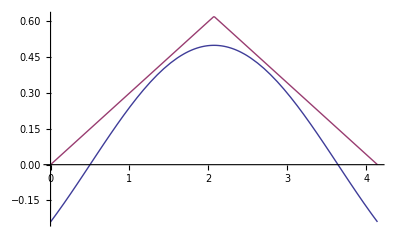

```mathematica
Plot[{.5Sin[x-.5],e[x]},{x,0,Pi+1},PlotRange->Full]
```

```mathematica
norm=Integrate[e[x],{x,0,Pi+1}]
```

1.28646

```mathematica
int=Integrate[e[x]/norm,x]
```

Piecewise[{{0., x≤0.}, {0.116599 x^2, 0.<x≤2.0708}, {-1.-0.233198 (-4.14159 x+0.5 x^2), 2.0708<x≤4.14159}, {1., True}}]

```mathematica
int/.x->0
```

0.

```mathematica
int/.x->Pi+1
```

1.

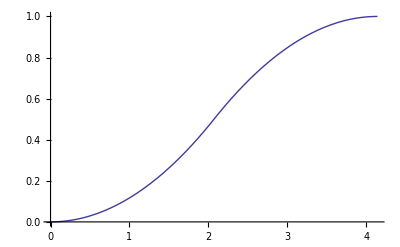

```mathematica
Plot[int/.x->y,{y,0,Pi+1}]
```

```mathematica
sol=Reduce[(int/.x->y)==z,y,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(z==0&&y≤0)||(0<z≤0.5&&y==2.92855 √z)||(0.5<z<0.5&&y==4.14159-1.86667×10^-15 √(2.46133×10^30-2.46133×10^30 z))||(z==0.5&&y==2.0708)||(0.5<z<1.&&y==4.14159-1.86667×10^-15 √(2.46133×10^30-2.46133×10^30 z))||(z==1.&&(y==4.14159||y>4.14159))

```mathematica
Manipulate[sol/.z->w,{w,0,1}]
```

```mathematica
1.8666702190894593*^-15Sqrt[2.4613284406667033*^30]
```

2.92855

```mathematica
4.14159-2.92855Sqrt[.5]
```

2.07079